/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

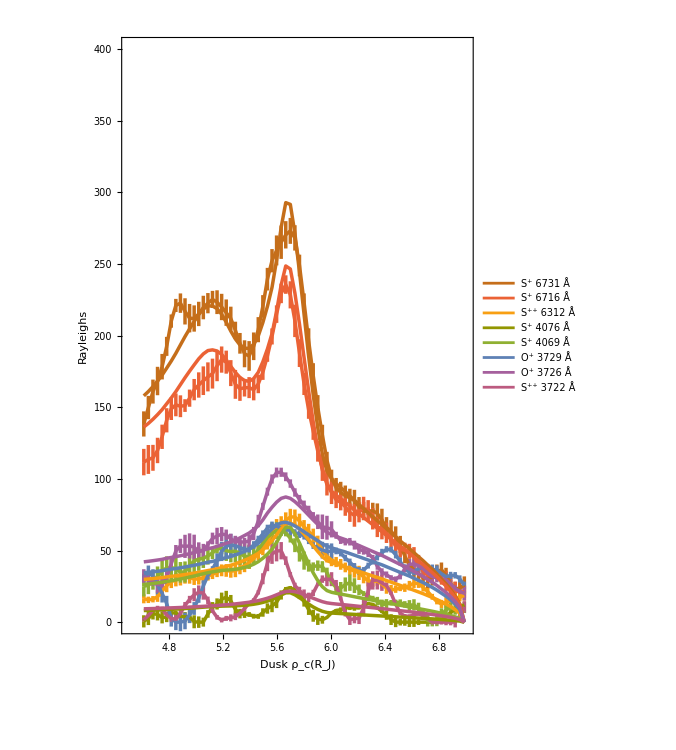

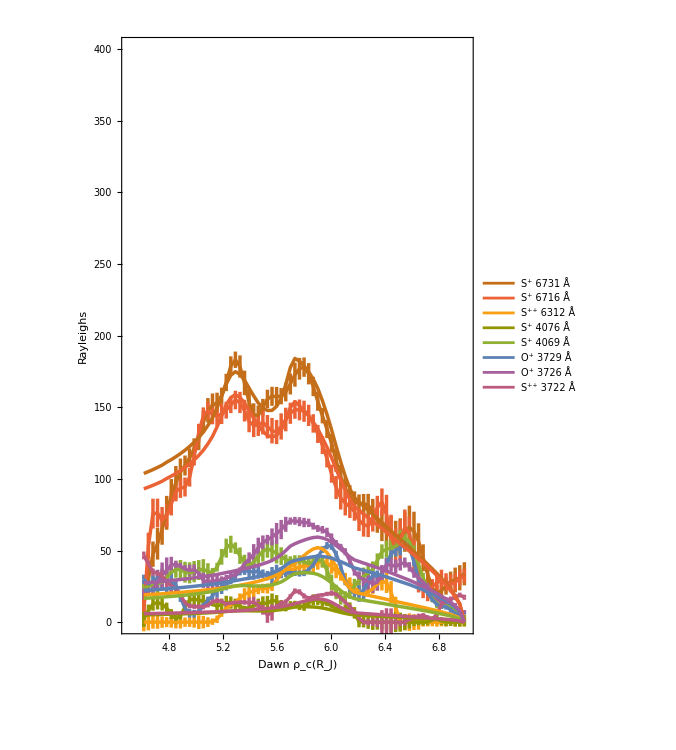

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night1_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night1_grid_to_plot_71x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night1_grid_to_plot_71x8.csv","CSV"]];
modeldusk = Import["night1_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night1_grid_to_plot_71x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night1_grid_to_plot_71x8.csv","CSV"]];
modeldawn = Import["night1_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];


duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];

dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];


duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];


dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night1_fixed.csv","CSV"]];

outsdusk = Transpose[ Import["night1_dusk_diffev_output_to_plot71x13.csv","CSV"]];

outsdawn = Transpose[ Import["night1_dawn_diffev_output_to_plot71x13.csv","CSV"]];


Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 



Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

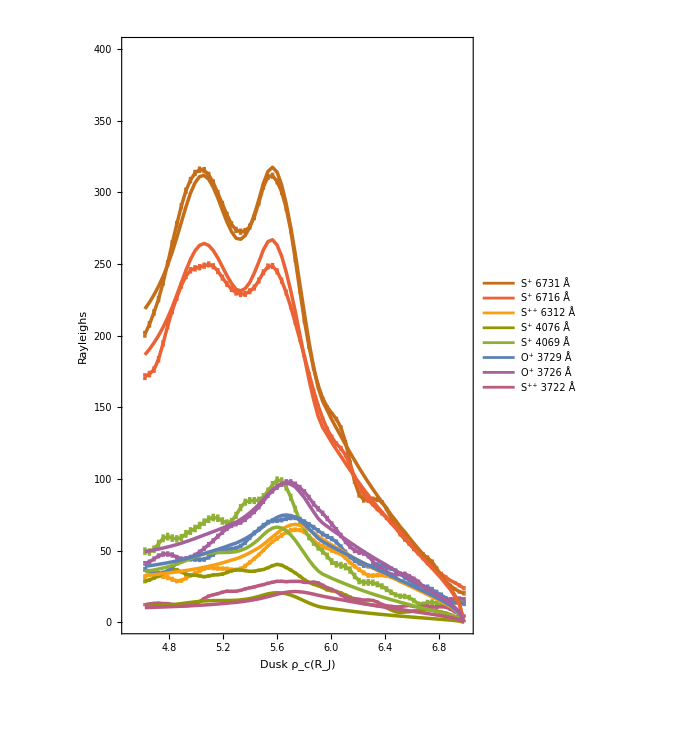

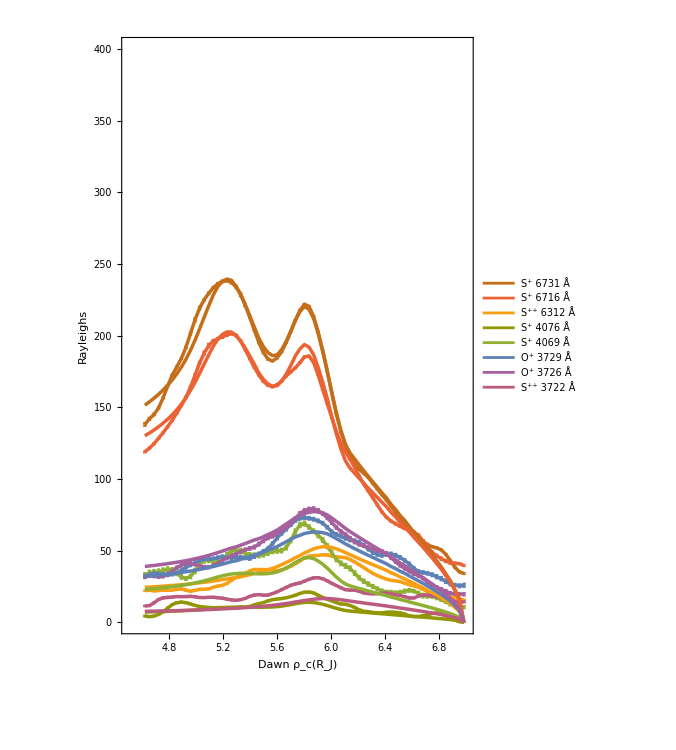

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night2_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night2_grid_to_plot_71x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night2_grid_to_plot_71x8.csv","CSV"]];
modeldusk = Import["night2_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night2_grid_to_plot_71x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night2_grid_to_plot_71x8.csv","CSV"]];
modeldawn = Import["night2_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];


duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];

dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];


duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];


dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night2_fixed.csv","CSV"]];

outsdusk = Transpose[ Import["night2_dusk_diffev_output_to_plot71x13.csv","CSV"]];

outsdawn = Transpose[ Import["night2_dawn_diffev_output_to_plot71x13.csv","CSV"]];


Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 



Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

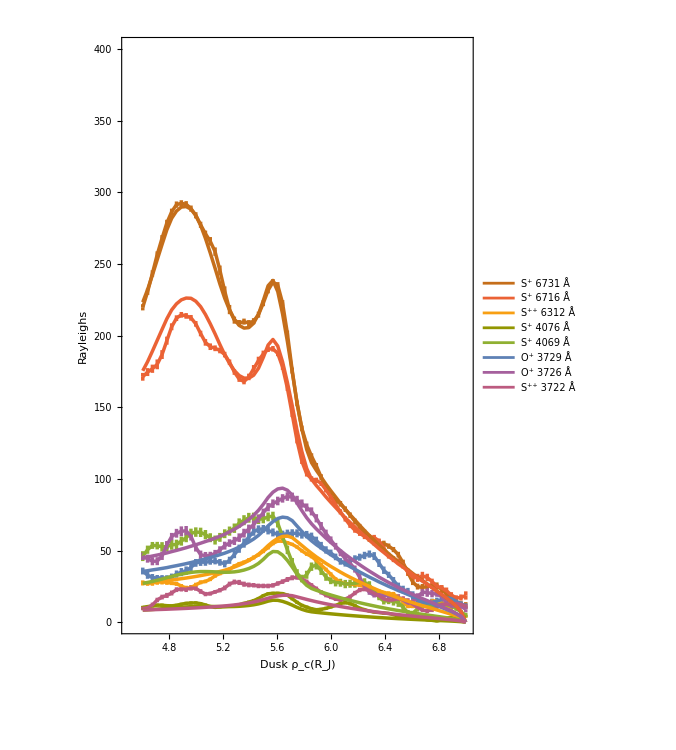

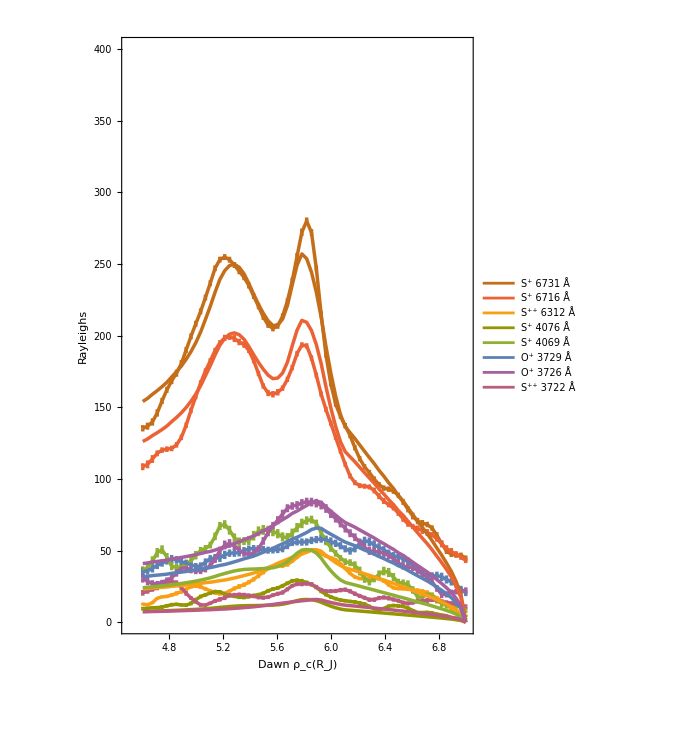

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night3_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night3_grid_to_plot_68x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night3_grid_to_plot_68x8.csv","CSV"]];
modeldusk = Import["night3_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night3_grid_to_plot_68x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night3_grid_to_plot_68x8.csv","CSV"]];
modeldawn = Import["night3_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];


duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];

dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];


duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];


dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night3_fixed.csv","CSV"]];

outsdusk = Transpose[ Import["night3_dusk_diffev_output_to_plot68x13.csv","CSV"]];

outsdawn = Transpose[ Import["night3_dawn_diffev_output_to_plot68x13.csv","CSV"]];


Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,1600}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 



Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

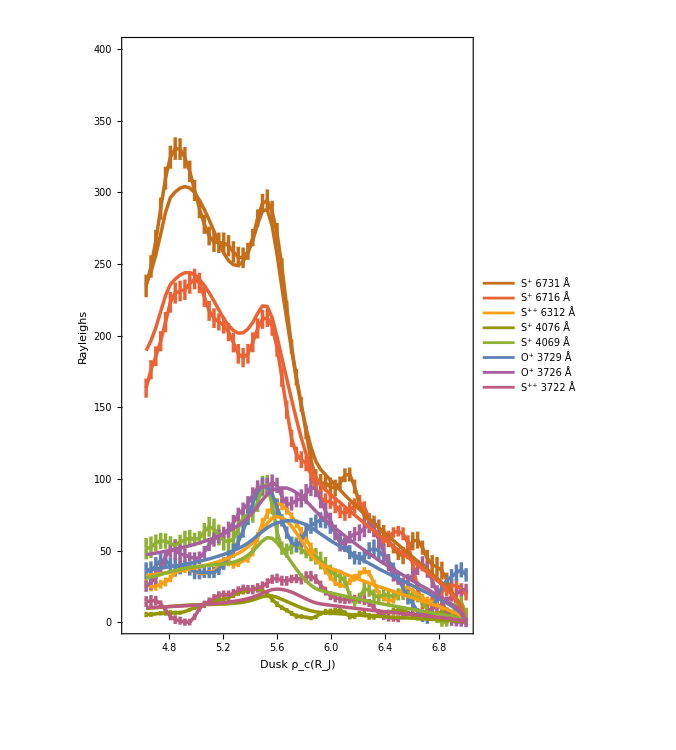

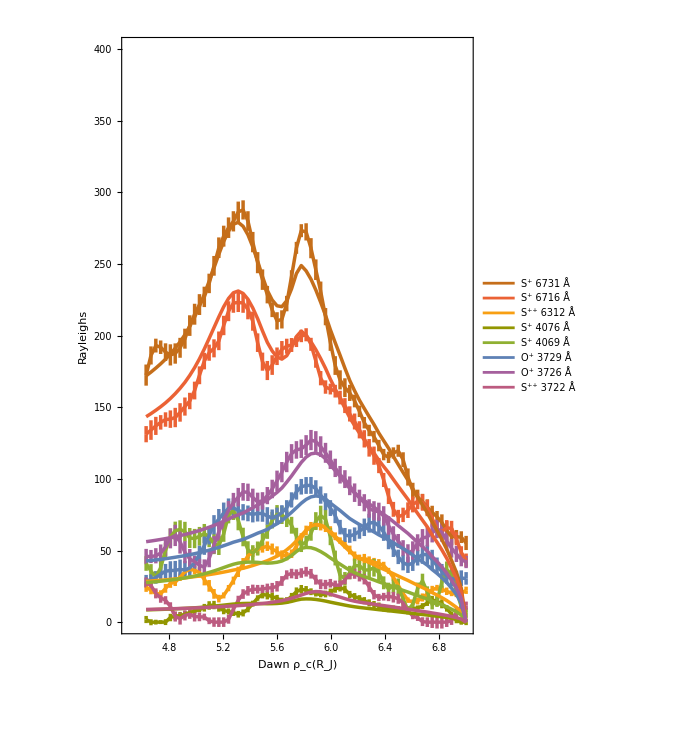

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night4_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night4_grid_to_plot_67x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night4_grid_to_plot_67x8.csv","CSV"]];
modeldusk = Import["night4_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night4_grid_to_plot_67x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night4_grid_to_plot_67x8.csv","CSV"]];
modeldawn = Import["night4_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];


duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];

dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];


duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];


dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night4_fixed.csv","CSV"]];

outsdusk = Transpose[ Import["night4_dusk_diffev_output_to_plot67x13.csv","CSV"]];

outsdawn = Transpose[ Import["night4_dawn_diffev_output_to_plot67x13.csv","CSV"]];


Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,1500}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,1.0}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 



Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

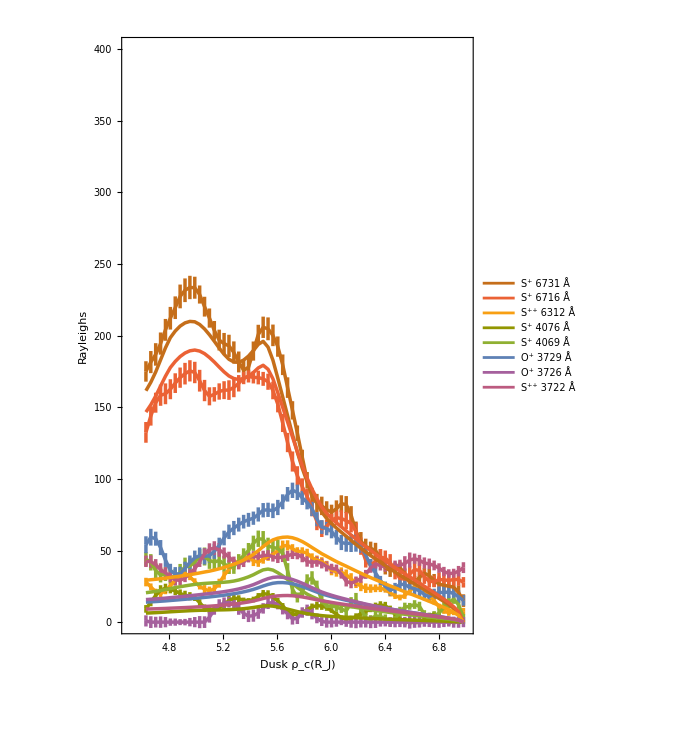

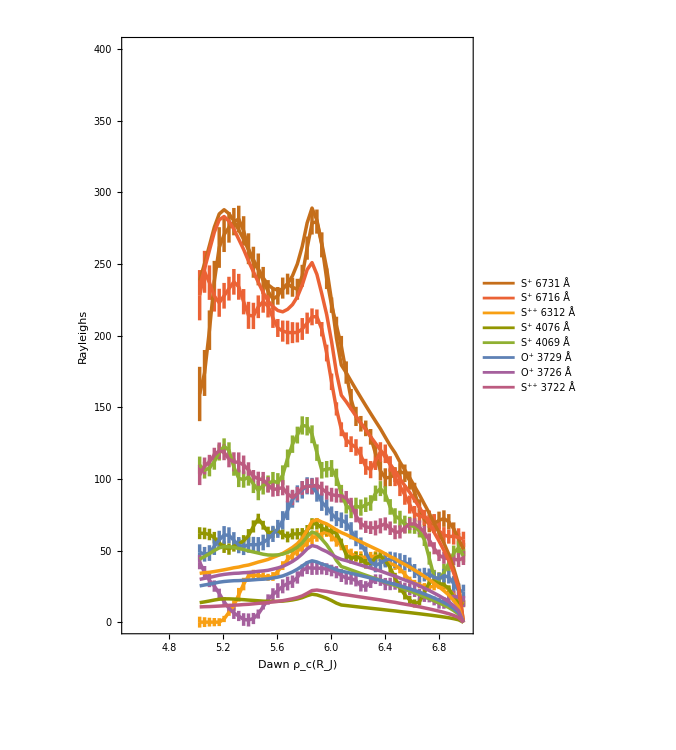

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρdusk= Flatten[Import["xgrid_night5_dusk_fixed.csv","CSV"]];
ρdawn= Flatten[Import["xgrid_night5_dawn_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night5_grid_to_plot_66x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night5_grid_to_plot_66x8.csv","CSV"]];
modeldusk = Import["night5_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night5_grid_to_plot_55x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night5_grid_to_plot_55x8.csv","CSV"]];
modeldawn = Import["night5_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];

ρ=ρdusk;
duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];
ρ=ρdawn;
dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];

ρ=ρdusk;
duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];

ρ=ρdawn;
dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρdusk= Flatten[Import["xgrid_night5_dusk_fixed.csv","CSV"]];
ρdawn= Flatten[Import["xgrid_night5_dawn_fixed.csv","CSV"]];
outsdusk = Transpose[ Import["night5_dusk_diffev_output_to_plot66x13.csv","CSV"]];

outsdawn = Transpose[ Import["night5_dawn_diffev_output_to_plot55x13.csv","CSV"]];

ρ=ρdusk;
Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,1100}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 

ρ=ρdawn;

Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

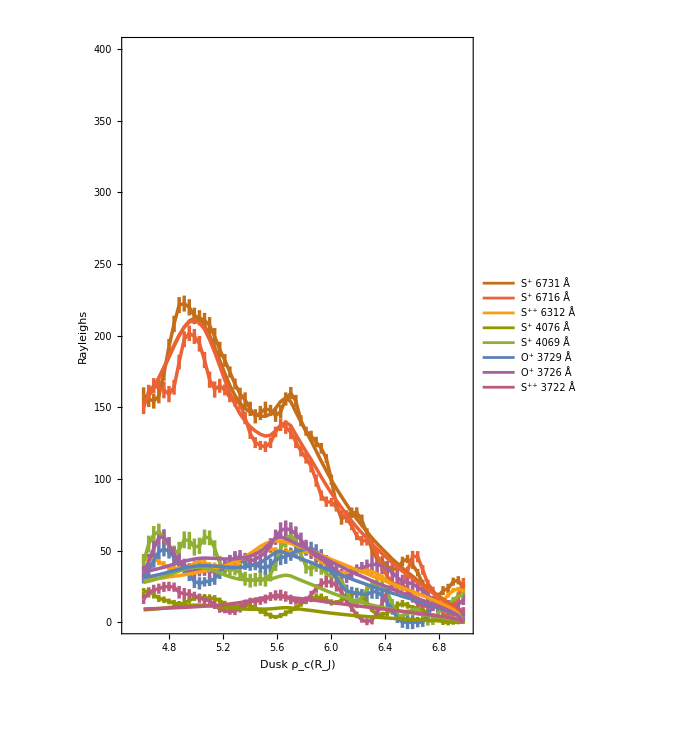

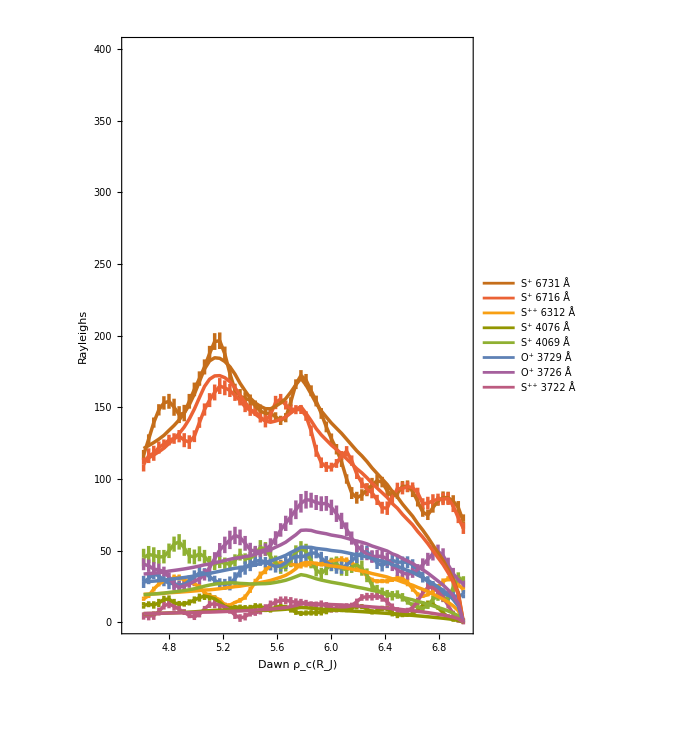

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night6_fixed.csv","CSV"]];


duskgrid = Transpose[ Import["Dusk_night6_grid_to_plot_64x8.csv","CSV"]];
errduskgrid = Transpose[ Import["err_Dusk_night6_grid_to_plot_64x8.csv","CSV"]];
modeldusk = Import["night6_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dusk_funcform_tec3partpl_python_60x8.csv","CSV"];



dawngrid = Transpose[ Import["Dawn_night6_grid_to_plot_64x8.csv","CSV"]];
errdawngrid = Transpose[ Import["err_Dawn_night6_grid_to_plot_64x8.csv","CSV"]];
modeldawn = Import["night6_varypls_varytec_locs_varyrhoRnsp_and_rhoRns2p_and_nop_diff_ev_model_dawn_funcform_tec3partpl_python_60x8.csv","CSV"];


duskdata1=Table[{ρ[[i]],Around[duskgrid [[i,1]],errduskgrid[[i,1]]]},{i,1,Length[ρ],1}];
duskdata2=Table[{ρ[[i]],Around[duskgrid [[i,2]],errduskgrid[[i,2]]]},{i,1,Length[ρ],1}];
duskdata3=Table[{ρ[[i]],Around[duskgrid [[i,3]],errduskgrid[[i,3]]]},{i,1,Length[ρ],1}];
duskdata4=Table[{ρ[[i]],Around[duskgrid [[i,4]],errduskgrid[[i,4]]]},{i,1,Length[ρ],1}];
duskdata5=Table[{ρ[[i]],Around[duskgrid [[i,5]],errduskgrid[[i,5]]]},{i,1,Length[ρ],1}];
duskdata6=Table[{ρ[[i]],Around[duskgrid [[i,6]],errduskgrid[[i,6]]]},{i,1,Length[ρ],1}];
duskdata7=Table[{ρ[[i]],Around[duskgrid [[i,7]],errduskgrid[[i,7]]]},{i,1,Length[ρ],1}];
duskdata8=Table[{ρ[[i]],Around[duskgrid [[i,8]],errduskgrid[[i,8]]]},{i,1,Length[ρ],1}];

dawndata1=Table[{ρ[[i]],Around[dawngrid [[i,1]],errdawngrid[[i,1]]]},{i,1,Length[ρ],1}];
dawndata2=Table[{ρ[[i]],Around[dawngrid [[i,2]],errdawngrid[[i,2]]]},{i,1,Length[ρ],1}];
dawndata3=Table[{ρ[[i]],Around[dawngrid [[i,3]],errdawngrid[[i,3]]]},{i,1,Length[ρ],1}];
dawndata4=Table[{ρ[[i]],Around[dawngrid [[i,4]],errdawngrid[[i,4]]]},{i,1,Length[ρ],1}];
dawndata5=Table[{ρ[[i]],Around[dawngrid [[i,5]],errdawngrid[[i,5]]]},{i,1,Length[ρ],1}];
dawndata6=Table[{ρ[[i]],Around[dawngrid [[i,6]],errdawngrid[[i,6]]]},{i,1,Length[ρ],1}];
dawndata7=Table[{ρ[[i]],Around[dawngrid [[i,7]],errdawngrid[[i,7]]]},{i,1,Length[ρ],1}];
dawndata8=Table[{ρ[[i]],Around[dawngrid [[i,8]],errdawngrid[[i,8]]]},{i,1,Length[ρ],1}];


duskmodel1=Table[{ρ[[i]],modeldusk[[i,1]]},{i,1,Length[ρ],1}];
duskmodel2=Table[{ρ[[i]],modeldusk[[i,2]]},{i,1,Length[ρ],1}];
duskmodel3=Table[{ρ[[i]],modeldusk[[i,3]]},{i,1,Length[ρ],1}];
duskmodel4=Table[{ρ[[i]],modeldusk[[i,4]]},{i,1,Length[ρ],1}];
duskmodel5=Table[{ρ[[i]],modeldusk[[i,5]]},{i,1,Length[ρ],1}];
duskmodel6=Table[{ρ[[i]],modeldusk[[i,6]]},{i,1,Length[ρ],1}];
duskmodel7=Table[{ρ[[i]],modeldusk[[i,7]]},{i,1,Length[ρ],1}];
duskmodel8=Table[{ρ[[i]],modeldusk[[i,8]]},{i,1,Length[ρ],1}];


dawnmodel1=Table[{ρ[[i]],modeldawn[[i,1]]},{i,1,Length[ρ],1}];
dawnmodel2=Table[{ρ[[i]],modeldawn[[i,2]]},{i,1,Length[ρ],1}];
dawnmodel3=Table[{ρ[[i]],modeldawn[[i,3]]},{i,1,Length[ρ],1}];
dawnmodel4=Table[{ρ[[i]],modeldawn[[i,4]]},{i,1,Length[ρ],1}];
dawnmodel5=Table[{ρ[[i]],modeldawn[[i,5]]},{i,1,Length[ρ],1}];
dawnmodel6=Table[{ρ[[i]],modeldawn[[i,6]]},{i,1,Length[ρ],1}];
dawnmodel7=Table[{ρ[[i]],modeldawn[[i,7]]},{i,1,Length[ρ],1}];
dawnmodel8=Table[{ρ[[i]],modeldawn[[i,8]]},{i,1,Length[ρ],1}];


thickval=0.005;


fsfs=12;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{40,40},{38,10}};


xpleg =0.83;
ypleg =0.65;


lfsize=22;
lmsize=18;

colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

p1=ListPlot[{duskdata8,duskdata7,duskdata6,duskdata5,duskdata4,duskdata3,duskdata2,duskdata1,duskmodel8,duskmodel7,duskmodel6,duskmodel5,duskmodel4,duskmodel3,duskmodel2,duskmodel1},Frame->True,PlotRange->{{4.5,7},{0,400}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{"Dusk ρ_c(R_J)","Rayleighs"},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

p2=ListPlot[{dawndata8,dawndata7,dawndata6,dawndata5,dawndata4,dawndata3,dawndata2,dawndata1,dawnmodel8,dawnmodel7,dawnmodel6,dawnmodel5,dawnmodel4,dawnmodel3,dawnmodel2,dawnmodel1},PlotRange->{{4.5,7},{0,400}},ImagePadding->impad,ImageSize->500,AspectRatio->1.5,FrameLabel->{{"Rayleighs",""},{"Dawn ρ_c(R_J)",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize],Scaled[{xpleg,ypleg}]],Joined->True]

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)



(*14,9,1,3,10,13,4,6*)
(*6,4,13,10,3,1,9,14*)

(*poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2}}] *)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]

ρ= Flatten[Import["xgrid_night6_fixed.csv","CSV"]];

outsdusk = Transpose[ Import["night6_dusk_diffev_output_to_plot64x13.csv","CSV"]];

outsdawn = Transpose[ Import["night6_dawn_diffev_output_to_plot64x13.csv","CSV"]];


Teclist=Table[{ρ[[i]],Around[outsdusk[[i,1]],outsdusk[[i,2]]]},{i,1,Length[ρ],1}];


neclist=Table[{ρ[[i]],Around[outsdusk[[i,3]],outsdusk[[i,4]]]},{i,1,Length[ρ],1}];


Nsplist=Table[{ρ[[i]],Around[outsdusk[[i,5]],outsdusk[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plist=Table[{ρ[[i]],Around[outsdusk[[i,7]],outsdusk[[i,8]]]},{i,1,Length[ρ],1}];


Noplist=Table[{ρ[[i]],Around[outsdusk[[i,9]],outsdusk[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlist=Table[{ρ[[i]],Around[outsdusk[[i,5]]/outsdusk[[i,3]],outsdusk[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlist=Table[{ρ[[i]],Around[outsdusk[[i,7]]/outsdusk[[i,3]],outsdusk[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlist=Table[{ρ[[i]],Around[outsdusk[[i,9]]/outsdusk[[i,3]],outsdusk[[i,13]]]},{i,1,Length[ρ],1}];



fsfs=8;
insetfontsize=fsfs;

(*{{left,right},{bottom,top}}*)

impad= {{32,32},{12,10}};



thickval=0.008;

p1=ListPlot[Teclist,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2=ListPlot[neclist,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3=ListPlot[Nsplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4=ListPlot[Nspmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5=ListPlot[Ns2plist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.1,600}]];

p6=ListPlot[Ns2pmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.08}]];


p7=ListPlot[Noplist,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,650}]];

p8=ListPlot[Nopmixlist,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)





poutsdusk=ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},FrameLabel->{"Dusk ρ_c(R_J)",""}] 



Teclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,1]],outsdawn[[i,2]]]},{i,1,Length[ρ],1}];


neclistdawn=Table[{ρ[[i]],Around[outsdawn[[i,3]],outsdawn[[i,4]]]},{i,1,Length[ρ],1}];


Nsplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]],outsdawn[[i,6]]]},{i,1,Length[ρ],1}];


Ns2plistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]],outsdawn[[i,8]]]},{i,1,Length[ρ],1}];


Noplistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]],outsdawn[[i,10]]]},{i,1,Length[ρ],1}];


Nspmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,5]]/outsdawn[[i,3]],outsdawn[[i,11]]]},{i,1,Length[ρ],1}];


Ns2pmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,7]]/outsdawn[[i,3]],outsdawn[[i,12]]]},{i,1,Length[ρ],1}];


Nopmixlistdawn=Table[{ρ[[i]],Around[outsdawn[[i,9]]/outsdawn[[i,3]],outsdawn[[i,13]]]},{i,1,Length[ρ],1}];



p1dawn=ListPlot[Teclistdawn,Frame->True,PlotRange->{{4.5,7},{0,10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["T_ec (eV)",Bold,FontSize->insetfontsize],{5.8,8}]];

p2dawn=ListPlot[neclistdawn,PlotRange->{{4.5,7},{0,4000}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_ec (cm^-3)",Bold,FontSize->insetfontsize],{6.4,3700}]];

p3dawn=ListPlot[Nsplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.4,600}]];

p4dawn=ListPlot[Nspmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.8}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];


p5dawn=ListPlot[Ns2plistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(S^(++)) (cm^-3)",Bold,FontSize->insetfontsize],{5.3,600}]];

p6dawn=ListPlot[Ns2pmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.4}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(S^(++)))/n_ec",Bold,FontSize->insetfontsize],{6.2,0.08}]];


p7dawn=ListPlot[Noplistdawn,Frame->True,PlotRange->{{4.5,7},{0,800}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,ScalingFunctions->{"Linear","Linear"},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["n_(O^+) (cm^-3)",Bold,FontSize->insetfontsize],{6.6,650}]];

p8dawn=ListPlot[Nopmixlistdawn,Frame->True,PlotRange->{{4.5,7},{0,0.6}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{{"",""},{"",""}},FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],Frame->True,FrameTicks->{{Automatic,All},{Automatic,Automatic}},Joined->True,PlotStyle->Thickness[thickval],Epilog->Inset[Style["(n_(O^+))/n_ec",Bold,FontSize->insetfontsize],{6.4,0.4}]];

(*Grid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}}]


GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6},{p7,p8}},Spacings->{0, 0}]*)

poutsdawn=ResourceFunction["PlotGrid"][{{p1dawn,p2dawn},{p3dawn,p4dawn},{p5dawn,p6dawn},{p7dawn,p8dawn}},FrameLabel->{"Dawn ρ_c (R_J)",""}]
```

/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

-Graphics-

-Graphics-